```mathematica
X=First[Import["import_data.xlsx"]];
```

```mathematica
s2 = {0.00049036,0.000216512, 0.000385349, 0.000418047, 0.000742115, 0.000760073, 0.000347548}
```

{0.00049036,0.000216512,0.000385349,0.000418047,0.000742115,0.000760073,0.000347548}

```mathematica
S=Covariance[X];
```

XX - центрирование и нормализация данных

```mathematica
XX=Standardize[X,Mean,1&];
```

```mathematica
SS=Covariance[XX];
```

```mathematica
logLambda=(165/2)*Log[Det[S]]-(165/2)*(Log[s2[[1]]]+Log[s2[[2]]]+Log[s2[[3]]]+Log[s2[[4]]]+Log[s2[[5]]]+Log[s2[[6]]]+Log[s2[[7]]])
```

-109.167

```mathematica
ro = 1-(2*7+11)/(6*165)//N
```

0.974747

```mathematica
theta = -2*ro*logLambda
```

212.821

Находим собственные векторы и собственные значения выборочной матрицы ковариации

```mathematica
ownLambda = Eigenvalues[SS]
```

{0.00128579,0.000755837,0.000394414,0.000324511,0.000269834,0.000188522,0.000141093}

```mathematica
ownVectors=Round[Eigenvectors[SS],0.001]
```

{{-0.357,-0.194,-0.436,-0.374,0.007,-0.693,-0.155},{0.058,-0.105,-0.001,-0.103,-0.986,0.049,-0.017},{0.872,0.083,0.054,-0.236,0.056,-0.32,-0.262},{0.151,0.136,-0.007,0.012,-0.038,-0.324,0.923},{0.051,0.174,-0.22,0.861,-0.12,-0.362,-0.179},{-0.288,0.59,0.647,-0.117,-0.082,-0.327,-0.151},{0.006,0.74,-0.583,-0.197,-0.044,0.266,-0.02}}

Нормируем собственные векторы

```mathematica
normOwnVectors ={};
```

```mathematica
For[i=1, i<=Length[ownLambda],i++, AppendTo[normOwnVectors, ownVectors[[i]]/(√ownLambda[[i]])]]
```

```mathematica
normOwnVectors
```

{{-9.95595,-5.41023,-12.1591,-10.43,0.195215,-19.3262,-4.32261},{2.10967,-3.81922,-0.0363736,-3.74648,-35.8643,1.7823,-0.618351},{43.9077,4.17929,2.71905,-11.8833,2.81976,-16.1129,-13.1924},{8.38229,7.54961,-0.388583,0.666142,-2.10945,-17.9858,51.2374},{3.10472,10.5926,-13.3929,52.4149,-7.30522,-22.0374,-10.8969},{-20.9755,42.9706,47.122,-8.52128,-5.97218,-23.8159,-10.9976},{0.505125,62.2988,-49.0814,-16.585,-3.70425,22.3939,-1.68375}}

```mathematica
Transpose[Last[normOwnVectors]].Last[normOwnVectors]
```

7083.48

```mathematica
1/Last[ownLambda]
```

7087.55

```mathematica
AllDisp = Total[ownLambda]
```

0.00336

```mathematica
Tr[SS]
```

0.00336

Вычисляем векторы факторных нагрузок

```mathematica
alpha ={};
```

```mathematica
For[i=1,i<=Length[ownLambda], i++,AppendTo[alpha, ownLambda[[i]]*normOwnVectors[[i]]]]
```

```mathematica
alpha
```

{{-0.0128013,-0.00695645,-0.0156341,-0.0134109,0.000251006,-0.0248496,-0.00555798},{0.00159456,-0.00288671,-0.0000274925,-0.00283173,-0.0271076,0.00134713,-0.000467372},{0.0173178,0.00164837,0.00107243,-0.00468693,0.00111215,-0.00635515,-0.00520328},{0.00272014,0.00244993,-0.000126099,0.00021617,-0.000684539,-0.00583659,0.0166271},{0.000837757,0.00285823,-0.00361386,0.0141433,-0.00197119,-0.00594643,-0.00294036},{-0.00395433,0.00810089,0.00888352,-0.00160645,-0.00112589,-0.00448982,-0.00207328},{0.0000712694,0.0087899,-0.00692501,-0.00234001,-0.000522642,0.00315961,-0.000237565}}

Доля дисперсии объясняемой каждой компонентой

```mathematica
For[i=1,i<=7,i++,Print[Part[ownLambda,i]/AllDisp, " ", i]]
```

0.382676 1

0.224951 2

0.117385 3

0.0965805 4

0.0803076 5

0.0561076 6

0.0419918 7

Доля дисперсии совокупностью компонент (двух, трех, ...)

```mathematica
s[1] = Part[ownLambda,1]/AllDisp;
```

```mathematica
s[2]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp
```

0.607628

```mathematica
s[3]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp
```

0.725013

```mathematica
s[4]= Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp
```

0.821593

```mathematica
s[5]= Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp+Part[ownLambda,5]/AllDisp
```

0.901901

```mathematica
s[6]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp+Part[ownLambda,5]/AllDisp+Part[ownLambda,6]/AllDisp
```

0.958008

```mathematica
s[7]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp+Part[ownLambda,5]/AllDisp+Part[ownLambda,6]/AllDisp+Part[ownLambda,7]/AllDisp
```

1.

Отбор главных компонент
1) По доле выделенной дисперсии

```mathematica
i=1;
```

```mathematica
While[s[i]<=0.7, Print[s[i+ 1], " ", i+1]; i++]
```

0.607628 2

0.725013 3

2) Критерий  Кайзера

```mathematica
i=1;
```

```mathematica
While[Part[ownLambda, i]*7/Tr[SS]>=1, Print[Part[ownLambda, i]*7/Tr[SS]]; i++]
```

2.67873

1.57466

3) Критерий каменистой осыпи

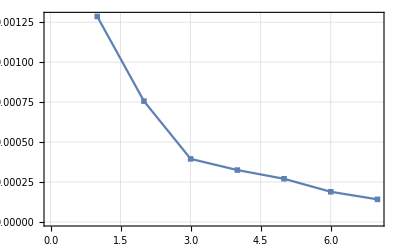

```mathematica
ListPlot[ownLambda, Frame->True,GridLines->Automatic,PlotLegends->"lambda", Joined->True,PlotMarkers->{■, 20}]
```

Будет выбрано две главных компоненты:

```mathematica
f1 = XX.Transpose[normOwnVectors[[1]]];
f2 = XX.Transpose[normOwnVectors[[2]]];
f3 = XX.Transpose[normOwnVectors[[3]]];
```

Находим значения обобщенных факторов через исходные признаки

```mathematica
Subscript[f, 1] =Subscript[β^(1), 1] Subscript[ξ, 1]+Subscript[β^(1), 2] Subscript[ξ, 2]+Subscript[β^(1), 3] Subscript[ξ, 3]+Subscript[β^(1), 4] Subscript[ξ, 4]+Subscript[β^(1), 5] Subscript[ξ, 5]+Subscript[β^(1), 6] Subscript[ξ, 6]+Subscript[β^(1), 7] Subscript[ξ, 7];
Subscript[f, 2] =Subscript[β^(2), 1] Subscript[ξ, 1]+Subscript[β^(2), 2] Subscript[ξ, 2]+Subscript[β^(2), 3] Subscript[ξ, 3]+Subscript[β^(2), 4] Subscript[ξ, 4]+Subscript[β^(2), 5] Subscript[ξ, 5]+Subscript[β^(2), 6] Subscript[ξ, 6]+Subscript[β^(2), 7] Subscript[ξ, 7];
Subscript[f, 2] =Subscript[β^(3), 1] Subscript[ξ, 1]+Subscript[β^(3), 2] Subscript[ξ, 2]+Subscript[β^(3), 3] Subscript[ξ, 3]+Subscript[β^(3), 4] Subscript[ξ, 4]+Subscript[β^(3), 5] Subscript[ξ, 5]+Subscript[β^(3), 6] Subscript[ξ, 6]+Subscript[β^(3), 7] Subscript[ξ, 7];
```

Разложим исходные признаки через обобщенные факторы

```mathematica
Subscript[ξ, 1]=Subscript[α^(1), 1] f^(1)+Subscript[α^(2), 1] f^(2)+Subscript[α^(3), 7] f^(3)
Subscript[ξ, 2]=Subscript[α^(1), 2] f^(1)+Subscript[α^(2), 2] f^(2)+Subscript[α^(3), 7] f^(3)
Subscript[ξ, 3]=Subscript[α^(1), 3] f^(1)+Subscript[α^(2), 3] f^(2)+Subscript[α^(3), 7] f^(3)
Subscript[ξ, 4]=Subscript[α^(1), 4] f^(1)+Subscript[α^(2), 4] f^(2)+Subscript[α^(3), 7] f^(3)
Subscript[ξ, 5]=Subscript[α^(1), 5] f^(1)+Subscript[α^(2), 5] f^(2)+Subscript[α^(3), 7] f^(3)
Subscript[ξ, 6]=Subscript[α^(1), 6] f^(1)+Subscript[α^(2), 6] f^(2)+Subscript[α^(3), 7] f^(3)
Subscript[ξ, 7]=Subscript[α^(1), 7] f^(1)+Subscript[α^(2), 7] f^(2)+Subscript[α^(3), 7] f^(3)
```

```mathematica
f1 = XX.Transpose[normOwnVectors[[1]]];
f2 = XX.Transpose[normOwnVectors[[2]]];
f3 = XX.Transpose[normOwnVectors[[3]]];
```

Матрица собственных векторов

```mathematica
B=ownVectors;
```

```mathematica
alpha1=alpha[[1]]
```

{-0.0128013,-0.00695645,-0.0156341,-0.0134109,0.000251006,-0.0248496,-0.00555798}

```mathematica
alpha2=alpha[[2]]
```

{0.00159456,-0.00288671,-0.0000274925,-0.00283173,-0.0271076,0.00134713,-0.000467372}

```mathematica
alpha3=alpha[[3]]
```

{0.0173178,0.00164837,0.00107243,-0.00468693,0.00111215,-0.00635515,-0.00520328}

Создание списка для визуализации

```mathematica
dataAlpha={};
dataF ={};
```

```mathematica
For[i=1,i<=Length[alpha1],i++,AppendTo[dataAlpha,{alpha1[[i]],alpha2[[i]]}]]
For[i=1,i<=Length[f1],i++,AppendTo[dataF,{f1[[i]],f2[[i]]}]]
```

```mathematica
dataAlpha
```

{{-0.0128013,0.00159456},{-0.00695645,-0.00288671},{-0.0156341,-0.0000274925},{-0.0134109,-0.00283173},{0.000251006,-0.0271076},{-0.0248496,0.00134713},{-0.00555798,-0.000467372}}

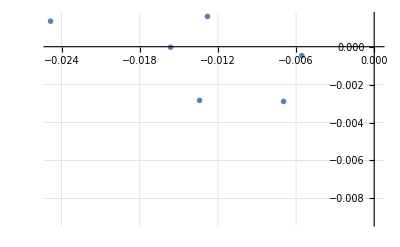

```mathematica
ListPlot[dataAlpha,GridLines->Automatic,PlotLegends->Automatic,PlotMarkers->{x, 20}]
```

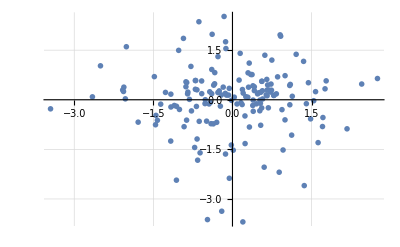

```mathematica
ListPlot[dataF, GridLines->Automatic,PlotLegends->Automatic,PlotMarkers->{o, 20}]
```

Для анализа обобщенных факторов воспользуемся критерием варимакс

```mathematica
k=7;m=2;
```

```mathematica
f[x_]:=dataAlpha.{{Cos[x], -Sin[x]},{Sin[x],Cos[x]}};
```

```mathematica
g[x_]:=dataF.Transpose[{{Cos[x], -Sin[x]},{Sin[x],Cos[x]}}];
```

```mathematica
plots={};
```

```mathematica
For[i=0 ,i<=10, i+=0.1,AppendTo[plots,ListPlot[f[i],GridLines->Automatic,PlotLegends->i,PlotMarkers->{o, 20}]]]
```

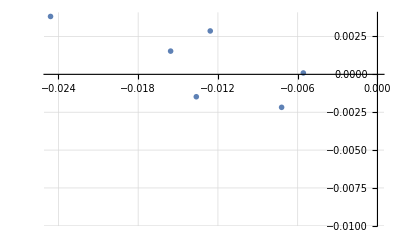
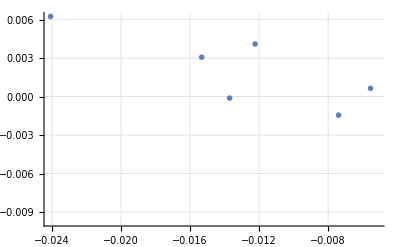
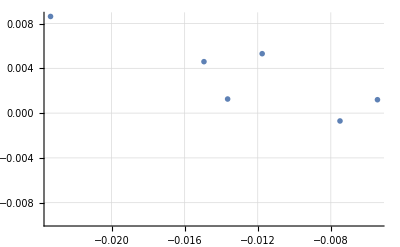
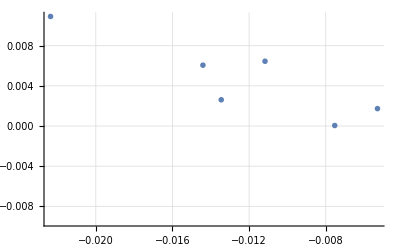
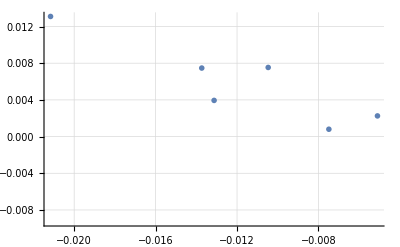
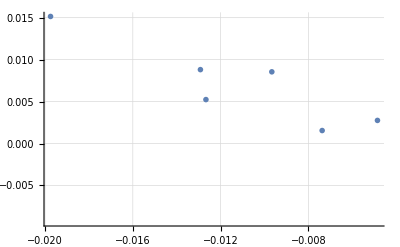
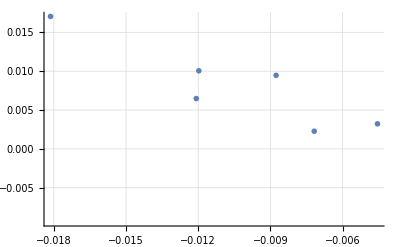
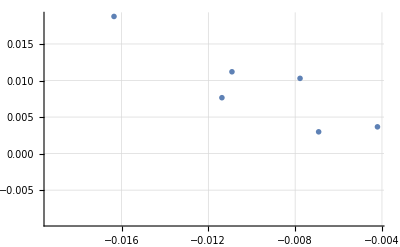
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots
```

```mathematica
varimax = Sum[1/k*(Sum[((alpha[[j]][[i]])^2-Mean[alpha[[j]]^2])^2,{i,1,k}]),{j,1,m}]
```

1.03739×10^-7

```mathematica
varimaxScore={};
```

```mathematica
For[a=0 ,a<=10, a+=0.1,AppendTo[varimaxScore, Sum[1/k*(Sum[((f[a][[i]][[j]])^2-1/k*Sum[(f[a][[m]][[j]])^2,{m, 1, k}])^2,{i,1,k}]),{j,1,m}]]]
```

```mathematica
varimaxScore
```

{1.03739×10^-7,1.00332×10^-7,9.19207×10^-8,7.98322×10^-8,6.59752×10^-8,5.25375×10^-8,4.16406×10^-8,3.50049×10^-8,3.3678×10^-8,3.78694×10^-8,4.69174×10^-8,5.93935×10^-8,7.33279×10^-8,8.65208×10^-8,9.68893×10^-8,1.02796×10^-7,1.0331×10^-7,9.83477×10^-8,8.86942×10^-8,7.58732×10^-8,6.19088×10^-8,4.90056×10^-8,3.92009×10^-8,3.40425×10^-8,3.43449×10^-8,4.00603×10^-8,5.02863×10^-8,6.34086×10^-8,7.73554×10^-8,8.99248×10^-8,9.91323×10^-8,1.03524×10^-7,1.02408×10^-7,9.59581×10^-8,8.51943×10^-8,7.18155×10^-8,5.7934×10^-8,4.57412×10^-8,3.71623×10^-8,3.35516×10^-8,3.54791×10^-8,4.26405×10^-8,5.39053×10^-8,6.7495×10^-8,8.1264×10^-8,9.30385×10^-8,1.0096×10^-7,1.03777×10^-7,1.01045×10^-7,9.3196×10^-8,8.14686×10^-8,6.77145×10^-8,5.4105×10^-8,4.27889×10^-8,3.55526×10^-8,3.35387×10^-8,3.70651×10^-8,4.55751×10^-8,5.7725×10^-8,7.15968×10^-8,8.50003×10^-8,9.58195×10^-8,1.02346×10^-7,1.0355×10^-7,9.92408×10^-8,9.0099×10^-8,7.75679×10^-8,6.36259×10^-8,5.0474×10^-8,4.01887×10^-8,3.43938×10^-8,3.40042×10^-8,3.90814×10^-8,4.88239×10^-8,6.16934×10^-8,7.56582×10^-8,8.85136×10^-8,9.82299×10^-8,1.03273×10^-7,1.02847×10^-7,9.70193×10^-8,8.67095×10^-8,7.35454×10^-8,5.96055×10^-8,4.70905×10^-8,3.79762×10^-8,3.37017×10^-8,3.49417×10^-8,4.15005×10^-8,5.23426×10^-8,6.57563×10^-8,7.96238×10^-8,9.17558×10^-8,1.00237×10^-7,1.03728×10^-7,1.01678×10^-7,9.44109×10^-8,8.30735×10^-8,6.9456×10^-8,5.57081×10^-8,4.40006×10^-8}

```mathematica
Position[varimaxScore,Max[varimaxScore]]
```

{{48}}

```mathematica
varimaxScore[[48]]
```

1.03777×10^-7

Новая матрица факторных нагрузок

```mathematica
newAlpha=f[4.8];
```

Оценки новых обобщенных факторов

```mathematica
newF=g[4.8];
```

В новой системе координат исходные признаки будут расположены следующим образом

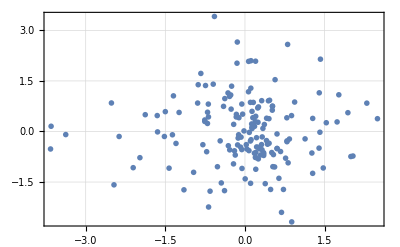

```mathematica
ListPlot[newF, Frame->True,GridLines->Automatic,PlotLegends->Automatic,PlotMarkers->{x, 20}]
```

Оценим долю  дисперсии  ξ_i, объясняемая фактором  f^(1)

```mathematica
df1 = {};
```

```mathematica
For[i=1, i<=7,i++,Round[AppendTo[ df1, (dataAlpha[[All,1]][[i]])^2/s2[[i]]],0.001]]
```

```mathematica
df1
```

{0.334189,0.223508,0.634293,0.430219,0.0000848978,0.812424,0.0888832}

Оценим долю  дисперсии  ξ_i, объясняемая фактором  f^(2)

```mathematica
df2={};
```

```mathematica
For[i=1, i<=7,i++,Round[AppendTo[ df2, (dataAlpha[[All,2]][[i]])^2/s2[[i]]],0.001]]
```

```mathematica
df2
```

{0.00518525,0.038488,1.96144×10^-6,0.0191813,0.990173,0.00238762,0.000628509}

Оценим долю  дисперсии  ξ_i, объясняемая фактором  f^(3)

```mathematica
df3={};
```

```mathematica
For[i=1, i<=7,i++,Round[ AppendTo[df3, alpha3[[i]]^2/s2[[i]]]]]
```

```mathematica
df3
```

{0.611604,0.0125495,0.0029846,0.0525474,0.0016667,0.053137,0.0779005}

```mathematica
Sum[{df1[[i]]+df2[[i]]+df3[[i]]},{i,1,7}]
```

{4.39204}

```mathematica
df={};
```

```mathematica
For[i=1, i<=7,i++,AppendTo[df,df1[[i]]+df2[[i]]+df3[[i]]]]
```

```mathematica
df
```

{0.950978,0.274545,0.63728,0.501947,0.991924,0.867948,0.167412}

Посчитаем коэффициент информативности определяющих признаков для этих факторов

```mathematica
alpha1=alpha[[1]]
```

{-0.0128013,-0.00695645,-0.0156341,-0.0134109,0.000251006,-0.0248496,-0.00555798}

```mathematica
alpha2=alpha[[2]]
```

{0.00159456,-0.00288671,-0.0000274925,-0.00283173,-0.0271076,0.00134713,-0.000467372}

```mathematica
alpha3=alpha[[3]]
```

{0.0173178,0.00164837,0.00107243,-0.00468693,0.00111215,-0.00635515,-0.00520328}

```mathematica
infF1 = (alpha1[[1]]^2+alpha1[[3]]^2+alpha1[[4]]^2+alpha1[[6]]^2)/Total[alpha1^2]
```

0.938252

```mathematica
infF2 = (alpha2[[2]]^2+alpha2[[4]]^2+alpha2[[1]]^2+alpha2[[5]]^2)/Sum[alpha2[[i]]^2,{i,1,7}]
```

0.997309

```mathematica
infF3= (alpha3[[1]]^2+alpha3[[2]]^2+alpha3[[7]]^2+alpha3[[6]]^2)/Sum[alpha3[[i]]^2,{i,1,7}]
```

0.938256

```mathematica
newAlpha1 = Transpose[newAlpha][[1]]
```

{-0.00270855,0.00226696,-0.00134058,0.00164743,0.0270256,-0.00351628,-0.0000207381}

```mathematica
newAlpha2 = Transpose[newAlpha][[2]]
```

{-0.0126127,-0.00718235,-0.0155765,-0.0136072,-0.00212184,-0.0246364,-0.00557756}

```mathematica
infF11 = (newAlpha1[[1]]^2+newAlpha1[[2]]^2+newAlpha1[[5]]^2+newAlpha1[[6]]^2)/(√Sum[newAlpha1[[i]]^2,{i,1,7}])
```

0.0273996

```mathematica
infF22 = (newAlpha2[[1]]^2+newAlpha2[[4]]^2+newAlpha2[[3]]^2+newAlpha2[[6]]^2)/(√Sum[newAlpha2[[i]]^2,{i,1,7}])
```

0.033355